# Collisional losses

## Trap lifetime

```mathematica
eqn={ρe'[t]==-Γ*ρe[t], ρe[0]==1};
```

```mathematica
sol=DSolve[eqn,ρe,t]
```

{{ρe→Function[{t},ⅇ^(-t Γ)]}}

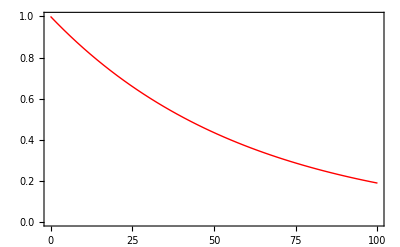

```mathematica
plot=Plot[ρe[t]/.sol /.{Γ->1/60}, {t, 0, 100}, PlotRange->{0, 1}]
```

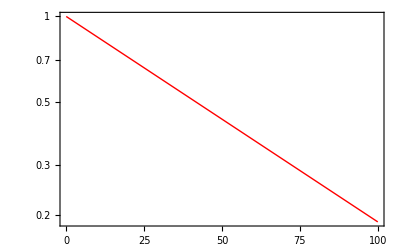

```mathematica
logplot=LogPlot[ρe[t]/.sol /.{Γ->1/60}, {t, 0, 100}, PlotRange->{0, 1}]
```

## Add excited-excited collisions

```mathematica
eqnee={ρe'[t]==-Γ*ρe[t]-γee*ρe[t]^2, ρe[0]==10^13};
```

```mathematica
solee=DSolve[eqnee,ρe,t]
```

{{ρe→Function[{t},(10000000000000 Γ)/(ⅇ^(t Γ) Γ-10000000000000 γee+10000000000000 ⅇ^(t Γ) γee)]}}

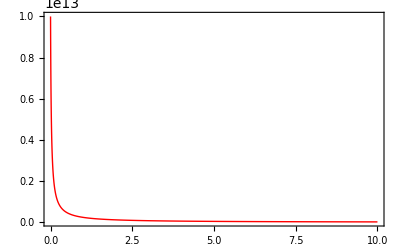

```mathematica
plotee=Plot[ρe[t]/.solee /.{Γ->1/60, γee-> 4*10^-12}, {t, 0, 10}, PlotRange->All]
```

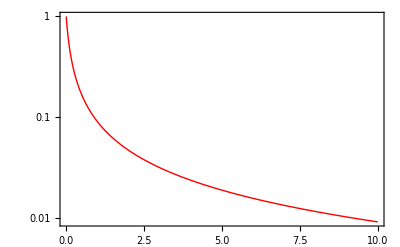

```mathematica
logplotee=LogPlot[ρe[t]/.solee /.{Γ->1/60, γee-> 1/0.1}, {t, 0, 10}, PlotRange->{0, 1}]
```

## Add excited-ground collisions

```mathematica
eqns={ρe'[t]==-γge*ρg[t]*ρe[t],ρg'[t]==-γge*ρe[t]*ρg[t],ρe[0]==1/3*10^13,ρg[0]==2/3*10^13};
solge=DSolve[eqns/.{γge-> 5.3*10^-13},{ρe,ρg},t]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

## One atom per tube

```mathematica
eqns1={ρe1'[t]==-Γ*ρe1[t]-γge*ρg1[t]*ρe1[t]-γee*ρe1[t]^2,ρg1'[t]==-Γ*ρg1[t]-γge*ρe1[t]*ρg1[t],ρe1[0]==1/3*10^13,ρg1[0]==2/3*10^13};
solge1=NDSolve[eqns1/.{Γ-> 0, γee-> 0, γge-> 0},{ρe1,ρg1},{t, 0, 5}]
```

{{ρe1→InterpolatingFunction[…],ρg1→InterpolatingFunction[…]}}

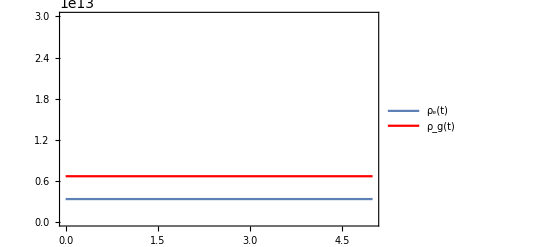

```mathematica
plotge1=Plot[Evaluate[{ρe1[t], ρg1[t]}/. First[solge1]], {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{0, 3*10^13}]
```

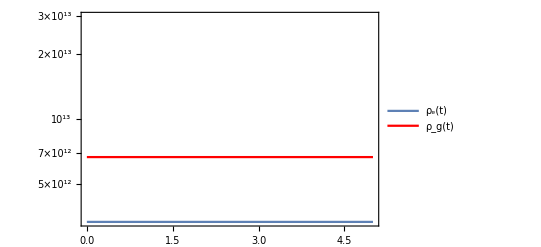

```mathematica
logplotge1=LogPlot[Evaluate[{ρe1[t], ρg1[t]}/. First[solge1]], {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{0, 3*10^13}]
```

## Two atoms per tube

```mathematica
eqns2={ρe2'[t]==-Γ*ρe2[t]-γge*ρg2[t]*ρe2[t]-γee*ρe2[t]^2,ρg2'[t]==-Γ*ρg2[t]-γge*ρe2[t]*ρg2[t],ρe2[0]==2*1/3*10^13,ρg2[0]==2*2/3*10^13};
solge2=NDSolve[eqns2/.{Γ-> 0, γee-> 4*10^-12, γge-> 0*5.3*10^-13},{ρe2,ρg2},{t, 0, 5}]
```

{{ρe2→InterpolatingFunction[…],ρg2→InterpolatingFunction[…]}}

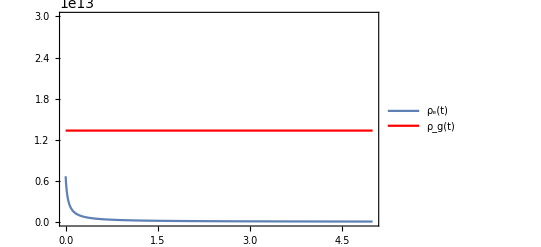

```mathematica
plotge2=Plot[Evaluate[{ρe2[t], ρg2[t]}/. First[solge2]], {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{0, 3*10^13}]
```

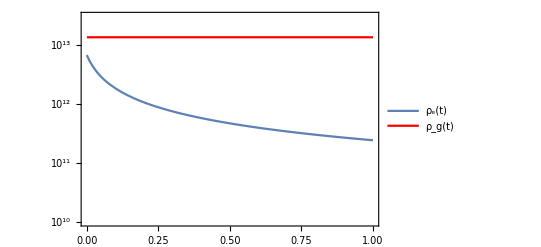

```mathematica
logplotge2=LogPlot[Evaluate[{ρe2[t], ρg2[t]}/. First[solge2]], {t, 0, 1}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{10^10, 3*10^13}]
```

## Three atoms per tube

```mathematica
eqns3={ρe3'[t]==-Γ*ρe3[t]-γge*ρg3[t]*ρe3[t]-γee*ρe3[t]^2,ρg3'[t]==-Γ*ρg3[t]-γge*ρe3[t]*ρg3[t],ρe3[0]==3*1/3*10^13,ρg3[0]==3*2/3*10^13};
solge3=NDSolve[eqns3/.{Γ-> 0, γee-> 4*10^-12, γge-> 5.3*10^-13},{ρe3,ρg3},{t, 0, 5}]
```

{{ρe3→InterpolatingFunction[…],ρg3→InterpolatingFunction[…]}}

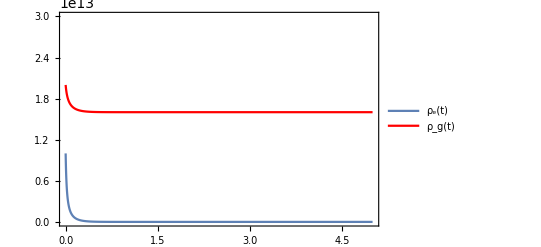

```mathematica
plotge3=Plot[Evaluate[{ρe3[t], ρg3[t]}/. First[solge3]], {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{0, 3*10^13}]
```

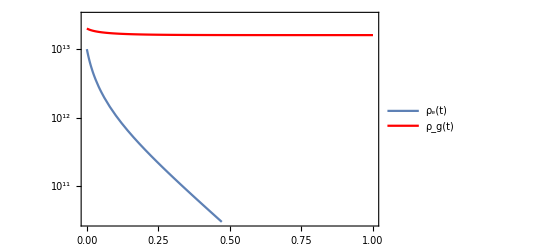

```mathematica
logplotge3=LogPlot[Evaluate[{ρe3[t], ρg3[t]}/. First[solge3]], {t, 0, 1}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{3*10^10, 3*10^13}]
```

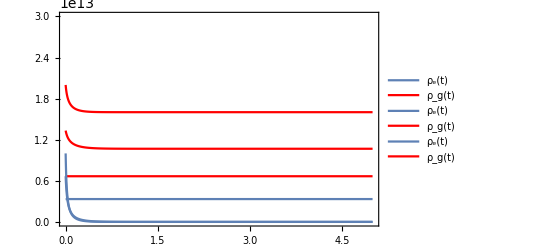

```mathematica
Show[plotge1, plotge2, plotge3]
```

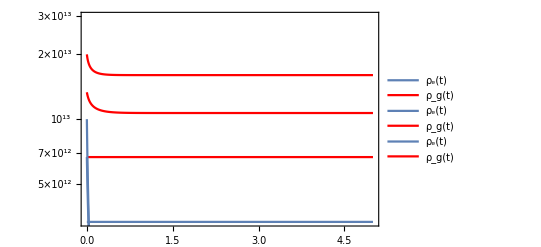

```mathematica
Show[logplotge1, logplotge2, logplotge3]
```

## Sum over lattice sites with different atom numbers

```mathematica
(* Distribution of number of atoms N per lattice site for an excitation ring on top of an elliptical density distribution *)
```

```mathematica
weight0=0.4664485759047779;
weight1=0.35440771640816743;
weight2=0.13594381837135222;
weight3=0.0350967834140144;
```

```mathematica
normweight1=weight1/(weight1+weight2+weight3)
normweight2=weight2/(weight1+weight2+weight3)
normweight3=weight3/(weight1+weight2+weight3)
```

0.674486

0.25872

0.066794

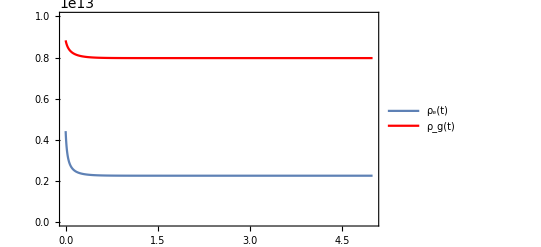

```mathematica
Plot[{normweight1*(ρe1[t]/.First[solge1])+normweight2*(ρe2[t]/.First[solge2])+normweight3*(ρe2[t]/.First[solge2]), normweight1*(ρg1[t]/.First[solge1])+normweight2*(ρg2[t]/.First[solge2])+normweight3*(ρg2[t]/.First[solge2])}, {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{0, 1*10^13}]
```

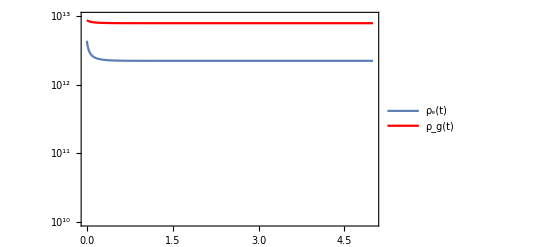

```mathematica
LogPlot[{normweight1*(ρe1[t]/.First[solge1])+normweight2*(ρe2[t]/.First[solge2])+normweight3*(ρe2[t]/.First[solge2]), normweight1*(ρg1[t]/.First[solge1])+normweight2*(ρg2[t]/.First[solge2])+normweight3*(ρg2[t]/.First[solge2])}, {t, 0, 5}, PlotLegends->{"ρ_e(t)", "ρ_g(t)"}, PlotRange->{10^10, 1*10^13}]
```

## Tests with toy parameters

```mathematica
eqn1={ρe'[t]==-γee*ρe[t]^2, ρe[0]==1};
```

```mathematica
sol1=DSolve[eqn1,ρe,t]
```

{{ρe→Function[{t},1/(1+t γee)]}}

```mathematica
eqn2={ρe'[t]==-γee*ρe[t]^2, ρe[0]==2};
```

```mathematica
sol2=DSolve[eqn2,ρe,t]
```

{{ρe→Function[{t},2/(1+2 t γee)]}}

```mathematica
eqn3={ρe'[t]==-γee*ρe[t]^2, ρe[0]==3};
```

```mathematica
sol3=DSolve[eqn3,ρe,t]
```

{{ρe→Function[{t},3/(1+3 t γee)]}}

```mathematica
plot1=LogPlot[(ρe[t]/.sol1 /.{γee-> 1}), {t, 0, 10}, PlotRange->{0, 1}];
```

```mathematica
plot2=LogPlot[((ρe[t]/.sol1 /.{γee-> 1})+(ρe[t]/.sol2 /.{γee-> 1}))/3, {t, 0, 10}, PlotRange->{0, 1}];
```

```mathematica
plot3=LogPlot[((ρe[t]/.sol1 /.{γee-> 1})+(ρe[t]/.sol2 /.{γee-> 1})+(ρe[t]/.sol3 /.{γee-> 1}))/6, {t, 0, 10}, PlotRange->{0, 1}];
```

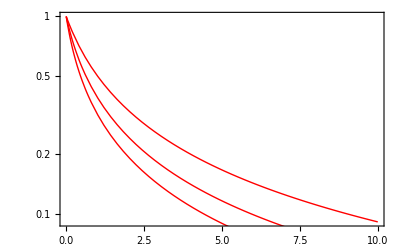

```mathematica
Show[plot1, plot2, plot3]
```

```mathematica
h=6.626070040*^-34;
kB=1.38064852*^-23;
amu=1.660539040*^-27;
ℏ=h/(2Pi);
m=88 amu;
ωr=2Pi 110*^3;
ωz=2Pi 200;
Tz=2*^-6;
```

```mathematica
Density[x_,y_,z_]:=(m ωr)/(π ℏ)*Exp[-(m ωr(x^2+y^2))/ℏ]*Sqrt[m ωz^2/(2 kB Tz)]/Sqrt[π]*Exp[-(m ωz^2 z^2)/(2kB Tz)];
```

```mathematica
ContourPlot3D[10^-6*Density[x*10^-6, y*10^-6, z*10^-6], {x, -0.1, 0.1}, {y, -0.1, 0.1}, {z, -10, 10}, PlotLegends->Automatic, AxesLabel->{"x (μm)", "y (μm)", "z (μm)"}, PlotLabel->"Density (cm^-3)"]
```

General::munfl: Exp[-1.91539×10^21] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.17838×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.91539×10^21] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Density[0, 0, 0]*10^-6
```

1.11175×10^13

```mathematica
eqn={ρe'[t]==-γee*ρe[t]^2, ρe[0]==a};
```

```mathematica
sol=DSolve[eqn,ρe,t]
```

{{ρe→Function[{t},a/(1+a t γee)]}}

```mathematica
Integrate[(ρe[t]/.sol /.{γee-> 1})*Density[x, y], {x, -10^-5, 10^-5}, {y, -10^-5, 10^-5}]
```

{1./(1+t)}

```mathematica
Integrate[Density[x, y], {x, -10^-5, 10^-5}, {y, -10^-5, 10^-5}]
```

1.

```mathematica
(* Loss coefficient in cm^3/s *)
kee = 4*10^-12;
```

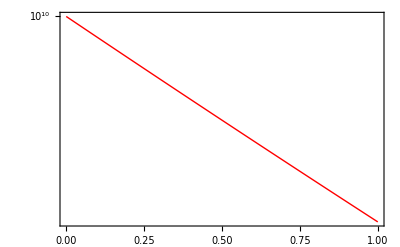

```mathematica
LogPlot[10^10/(1+10^10*kee*t), {t, 0, 1}, PlotRange->{0, 1*10^10}]
```

## Variation of atom number per lattice site across the cloud

```mathematica
LatticeWavelength=914*^-9;
AreaLattice=Pi(212.*^-6 114*^-6);
AreaLatticeSite=(LatticeWavelength/2)^2;
AreaPixel=(5.4*^-6)^2;
TotalAtomNumber=7.4*^5;

Sites=AreaLattice/AreaLatticeSite;
SitesPerPixel=AreaPixel/AreaLatticeSite;

NSite=TotalAtomNumber/Sites
NPixel=TotalAtomNumber/(AreaLattice/AreaPixel)

RadialTrapFrequency=2Pi 110*^3;
LongitudinalTrapFrequency=2Pi 200;
LongitudinalTemperature=2*^-6;
```

2.03551

284.203

```mathematica
σx=114*10^-6;
σy=212*10^-6;
```

```mathematica
Distribution[x_, y_] = 1/(Pi σx σy)*Exp[-(x^2/σx^2+y^2/σy^2)];
```

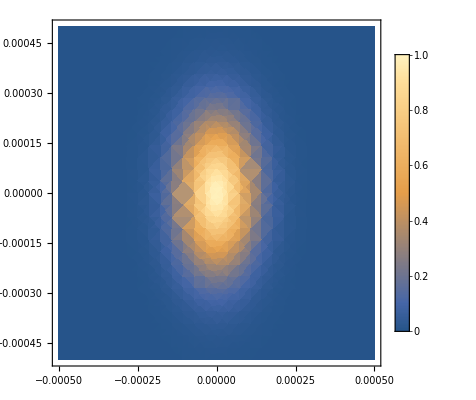

```mathematica
DensityPlot[Distribution[x, y]/Distribution[0, 0], {x, -500*10^-6, 500*10^-6}, {y, -500*10^-6, 500*10^-6}, PlotLegends->Automatic, PlotRange->Full]
```

```mathematica
NSiteCenter=Integrate[TotalAtomNumber*Distribution[x, y], {x, -5.4/2*10^-6, 5.4/2*10^-6}, {y, -5.4/2*10^-6, 5.4/2*10^-6}]/SitesPerPixel
```

2.03502

```mathematica
NSiteRing=Integrate[TotalAtomNumber*Distribution[x, y], {x, -19*5.4/2*10^-6, -18*5.4/2*10^-6}, {y, -5.4/2*10^-6, 5.4/2*10^-6}]/SitesPerPixel
```

0.839906